## Assignment 2

4.2.10(b,c)

(10)(a) Suppose that a tidal estuary extends from r=0 to r=a, where it meets the open sea. Suppose the floor of the estuary is level,  but its width is proportional to cylindrical radius r (a wedge-shaped estuary, like Moray Firth in Scotland; see Fig. 4.3). Then using the same method as that which led to Eq. (3.1.78), show that  the water depth z(r,t) satisfies the following wave equation:

∂^2/(∂t^2)z=g h 1/r∂/(∂r)(r∂/(∂r)z),

where g is the acceleration of gravity and h is the equilibrium depth. (Note that no θ dependence is assumed; boundary conditions along the upper and lower sides of the estuary are Neumann, so this θ-independent solution is allowed.)

Fig. 4.3 Exercise (10).

(b) The tidal motion of the open sea is represented by the following Dirichlet boundary condition at the end of the estuary:

z(a,t) = h + d Cos ω t.

Find a solution of the PDE that satisfies this boundary condition, along with the initial conditions
	 z(r,0)=h+d,  (∂z)/(∂t)(r,0)=0.

Animate z(r,t) for 5 days in 2 hour intervals taking a=1000 km, h=500 m, d=1 m and ω=2π/12 hours.

(c) Find values of ω for which z(r,t) increases without bound.

### Solution

#### (b)

First put the problem in standard form, z =u + Δz . Choose u(r,t) = h + d cos ω t, Then Δz satisfies c^2/r∂/(∂r)(r (∂Δz)/(∂r))=(∂^2 Δz)/(∂t^2)-ω^2 d cosω t. Write the solution for Δz in terms of eigenmodes ψ_n(r) that satisfy the ODE c^2/r∂/(∂r)(r (∂ψ_n)/(∂r))=-ω_n^2 ψ_n, with boundary conditions ψ(a)=0. This is a Bessel equation, with solution
		ψ_n(r) = J_o(ω_n/c r). To satisfy the boundary conditions, we require ω_n = c j_(o n)/a. The solution for Δz(r,t) follows:

```mathematica
Clear["Global`*"]
```

```mathematica
ψ[n_,r_] = BesselJ[0,j[n] r/a];
```

```mathematica
ωn[n_] = j[n] c/a;
```

```mathematica
j[n_]:= (j[n]=BesselJZero[0,n]//N)/;n∈Integers
```

```mathematica
s[n_,t_] = ω^2 d Cos[ω t]Integrate[ ψ[n,r] r,{r,0,a}]/Integrate[ ψ[n,r]^2 r,{r,0,a}]
```

(2 d ω^2 BesselJ[1,j[n]] Cos[t ω])/((BesselJ[0,j[n]]^2+BesselJ[1,j[n]]^2) j[n])

```mathematica
DSolve[{c[n]''[t] == -ωn[n]^2 c[n][t] + s[n,t],c[n][0]==0,c[n]'[0]==0},c[n][t],t]
```

{{c[n][t]→(2 (-a^2 d ω^2 BesselJ[1,j[n]] Cos[(c t j[n])/a]+a^2 d ω^2 BesselJ[1,j[n]] Cos[t ω] Cos[(c t j[n])/a]^2+a^2 d ω^2 BesselJ[1,j[n]] Cos[t ω] Sin[(c t j[n])/a]^2))/((BesselJ[0,j[n]]^2+BesselJ[1,j[n]]^2) j[n] (-a^2 ω^2+c^2 j[n]^2))}}

```mathematica
c[n_][t_] = c[n][t]/.%[[1]];
```

```mathematica
Δz[r_,t_] = Sum[c[n][t] ψ[n,r],{n,1,10}];
```

```mathematica
z[r_,t_] = h + d Cos [ω t] + Δz[r,t];
```

Use parameters and plot

```mathematica
a=1000 1000; g=9.8; ω = 2 Pi/(12 3600); d = 1; h = 500; c = Sqrt[ g h];
```

```mathematica
day = 24 3600;
```

```mathematica
z[.1,.3]
```

501.

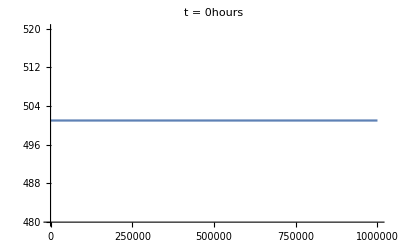
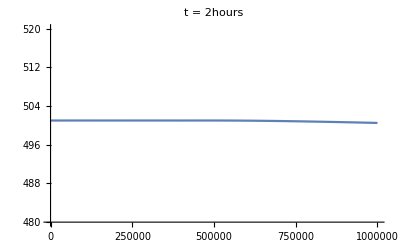
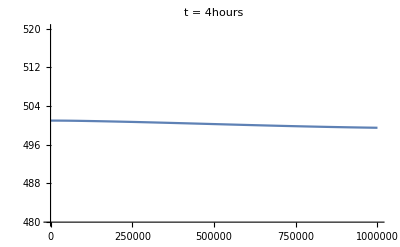
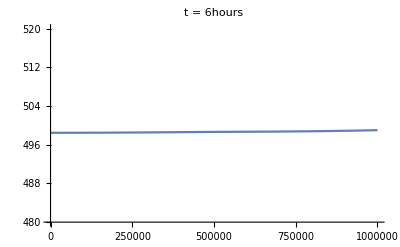
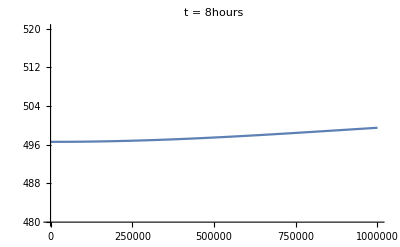
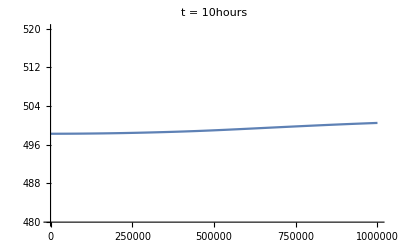
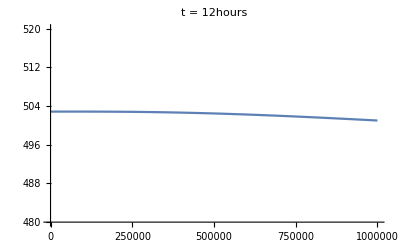
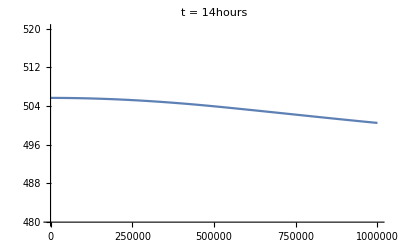

```mathematica
Table[Plot[z[r,t day],{r,0,a},PlotRange->{h-20d,h+20d},PlotLabel->"t = "<>ToString[24 t]<> "hours"],{t,0,4,1/12}]
```

```mathematica
ListAnimate[%]
```

Tides as high as 10 meters are obtained within the estuary.

#### (c)

Note the near-resonance behavior. The forcing frequency ω was almost the same as the lowest mode:

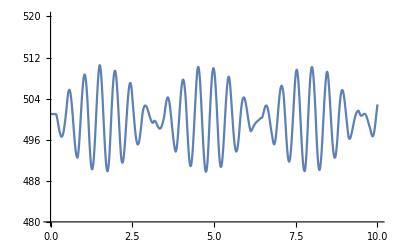

```mathematica
Plot[z[0,t day],{t,0,10 },PlotRange->{h-20d,h+20d}]
```

```mathematica
ω//N
```

0.000145444

```mathematica
ωn[1]
```

0.000168338

In resonance, if we assume that parameters are such that ω_n=ω then we expect secular growth of the solution.

```mathematica
Table[ ωn[m],{m,1,10}]
```

{0.000168338,0.000386405,0.000605761,0.000825407,0.00104516,0.00126497,0.00148481,0.00170467,0.00192454,0.00214442}

Forcing periods in hours fthat would cause secular growth:

```mathematica
(2Pi/%)/3600
```

{10.368,4.51683,2.88122,2.11451,1.66991,1.37973,1.17545,1.02385,0.90688,0.813892}

4.2.8

(8) A wedge, shown in Fig. 4.7, has opening angle α. The wedge is filled with uniform charge, ρ/ϵ_o=1 V/m^2. The walls of the wedge are grounded, at zero potential.

(a) Find the eigenmodes for this geometry.

(b) Use these eigenmodes to solve for the potential ϕ(r,θ) inside the wedge. Plot the solution using a contour plot for α=65 °.

### Solution

#### (a)

The Dirichlet eigenmodes for this geometry are of the form ψ(r,θ) = R(r) Θ(θ). The R part is the usual Bessel function, R = J_μ(j_(μ n) r/a). The θ part are of the general form
Θ(θ) =A sin μ θ +B cos μ θ. 
 Θ(θ=0)=Θ(θ=α)=0. Therefore, these modes are Θ(θ) = sin m π θ/α and μ = m π/α, m=1,2,3,... (note that μ is no longer an integer) . So

```mathematica
Clear["Global`*"]
```

```mathematica
ψ[m_,n_,r_,θ_] = BesselJ[m Pi/α,j[m , n] r/a] Sin[m Pi θ/α];
```

where j[m,n] is the nth zero of J_(m π/α)(r).  Corresponding eigenvalues are

```mathematica
λ[m_,n_] = -(j[m,n]/a)^2
```

-j[m,n]^2/a^2

```mathematica
j[m_,n_]:= (j[m,n]=BesselJZero[m Pi/α,n]//N)/;m∈Integers&&n∈Integers
```

#### (b)

The solution for ϕ is the usual Fourier expansion

```mathematica
c[m_,n_] = Integrate[ 1  ψ[m,n,r,θ] r,{r,0,a},{θ,0,α},Assumptions->m∈Integers&&0<α<2Pi]/Integrate[  ψ[m,n,r,θ]^2 r,{r,0,a},{θ,0,α},Assumptions-> m∈Integers&&0<α<2Pi] /λ[m,n]
```

ConditionalExpression[(2^(2-(m π+α)/α) (-1+(-1)^m) a^2 Gamma[1+(m π)/(2 α)] HypergeometricPFQRegularized[{1+(m π)/(2 α)},{2+(m π)/(2 α),1+(m π)/α},-1/4 j[m,n]^2] j[m,n]^(-2+(m π)/α))/(m π (BesselJ[1+(m π)/α,j[m,n]]^2+BesselJ[(m π)/α,j[m,n]]^2-(2 m π BesselJ[1+(m π)/α,j[m,n]] BesselJ[(m π)/α,j[m,n]])/(α j[m,n]))),m π+2 α>0&&((Re[j[m,n]]==0&&Im[j[m,n]]>0)||Re[j[m,n]]>0)&&j[m,n]≥0&&m π+α>0]

```mathematica
a=1;α=65 Degree;
```

```mathematica
ϕ[r_,θ_] = Sum[c[m,n] ψ[m,n,r,θ],{m,1,10},{n,1,10}]
```

0.-0.0991602 BesselJ[π/(65 °),6.09676 r] Sin[(π θ)/(65 °)]-0.000758069 BesselJ[π/(65 °),9.45496 r] Sin[(π θ)/(65 °)]-0.0114334 BesselJ[π/(65 °),12.6969 r] Sin[(π θ)/(65 °)]+0.000490838 BesselJ[π/(65 °),15.8974 r] Sin[(π θ)/(65 °)]-0.00367248 BesselJ[π/(65 °),19.078 r] Sin[(π θ)/(65 °)]+0.000380117 BesselJ[π/(65 °),22.2473 r] Sin[(π θ)/(65 °)]-0.00167429 BesselJ[π/(65 °),25.4096 r] Sin[(π θ)/(65 °)]+0.000262981 BesselJ[π/(65 °),28.5674 r] Sin[(π θ)/(65 °)]-0.000916772 BesselJ[π/(65 °),31.7219 r] Sin[(π θ)/(65 °)]+0.000185901 BesselJ[π/(65 °),34.8741 r] Sin[(π θ)/(65 °)]-0.0110309 BesselJ[(3 π)/(65 °),12.5735 r] Sin[(3 π θ)/(65 °)]-0.00150335 BesselJ[(3 π)/(65 °),16.4094 r] Sin[(3 π θ)/(65 °)]-0.00229258 BesselJ[(3 π)/(65 °),19.9414 r] Sin[(3 π θ)/(65 °)]-0.000453575 BesselJ[(3 π)/(65 °),23.3432 r] Sin[(3 π θ)/(65 °)]-0.000942628 BesselJ[(3 π)/(65 °),26.6735 r] Sin[(3 π θ)/(65 °)]-0.000189457 BesselJ[(3 π)/(65 °),29.9594 r] Sin[(3 π θ)/(65 °)]-0.000493465 BesselJ[(3 π)/(65 °),33.2153 r] Sin[(3 π θ)/(65 °)]-0.0000931469 BesselJ[(3 π)/(65 °),36.45 r] Sin[(3 π θ)/(65 °)]-0.000294957 BesselJ[(3 π)/(65 °),39.669 r] Sin[(3 π θ)/(65 °)]-0.0000505395 BesselJ[(3 π)/(65 °),42.876 r] Sin[(3 π θ)/(65 °)]-0.00353785 BesselJ[π/(13 °),18.7313 r] Sin[(π θ)/(13 °)]-0.000708255 BesselJ[π/(13 °),22.9378 r] Sin[(π θ)/(13 °)]-0.00093238 BesselJ[π/(13 °),26.7229 r] Sin[(π θ)/(13 °)]-0.000278067 BesselJ[π/(13 °),30.3164 r] Sin[(π θ)/(13 °)]-0.000435126 BesselJ[π/(13 °),33.7996 r] Sin[(π θ)/(13 °)]-0.000140591 BesselJ[π/(13 °),37.2111 r] Sin[(π θ)/(13 °)]-0.000247441 BesselJ[π/(13 °),40.5728 r] Sin[(π θ)/(13 °)]-0.0000810001 BesselJ[π/(13 °),43.8981 r] Sin[(π θ)/(13 °)]-0.000156877 BesselJ[π/(13 °),47.1956 r] Sin[(π θ)/(13 °)]-0.0000506982 BesselJ[π/(13 °),50.4715 r] Sin[(π θ)/(13 °)]-0.00162077 BesselJ[(7 π)/(65 °),24.7535 r] Sin[(7 π θ)/(65 °)]-0.000388964 BesselJ[(7 π)/(65 °),29.2667 r] Sin[(7 π θ)/(65 °)]-0.000488953 BesselJ[(7 π)/(65 °),33.2712 r] Sin[(7 π θ)/(65 °)]-0.00017448 BesselJ[(7 π)/(65 °),37.0372 r] Sin[(7 π θ)/(65 °)]-0.00024696 BesselJ[(7 π)/(65 °),40.6624 r] Sin[(7 π θ)/(65 °)]-0.0000969477 BesselJ[(7 π)/(65 °),44.1941 r] Sin[(7 π θ)/(65 °)]-0.000148415 BesselJ[(7 π)/(65 °),47.6594 r] Sin[(7 π θ)/(65 °)]-0.0000601579 BesselJ[(7 π)/(65 °),51.0753 r] Sin[(7 π θ)/(65 °)]-0.0000980824 BesselJ[(7 π)/(65 °),54.453 r] Sin[(7 π θ)/(65 °)]-0.0000400512 BesselJ[(7 π)/(65 °),57.8005 r] Sin[(7 π θ)/(65 °)]-0.000892313 BesselJ[(9 π)/(65 °),30.6969 r] Sin[(9 π θ)/(65 °)]-0.000238908 BesselJ[(9 π)/(65 °),35.475 r] Sin[(9 π θ)/(65 °)]-0.000294351 BesselJ[(9 π)/(65 °),39.6737 r] Sin[(9 π θ)/(65 °)]-0.000116656 BesselJ[(9 π)/(65 °),43.5958 r] Sin[(9 π θ)/(65 °)]-0.000157078 BesselJ[(9 π)/(65 °),47.3519 r] Sin[(9 π θ)/(65 °)]-0.000068886 BesselJ[(9 π)/(65 °),50.9963 r] Sin[(9 π θ)/(65 °)]-0.0000982471 BesselJ[(9 π)/(65 °),54.5603 r] Sin[(9 π θ)/(65 °)]-0.0000448475 BesselJ[(9 π)/(65 °),58.0637 r] Sin[(9 π θ)/(65 °)]-0.000066972 BesselJ[(9 π)/(65 °),61.5198 r] Sin[(9 π θ)/(65 °)]-0.0000310699 BesselJ[(9 π)/(65 °),64.9381 r] Sin[(9 π θ)/(65 °)]

```mathematica
ParametricPlot3D[{r Cos[θ], r Sin[θ],ϕ[r,θ]},{r,0,a},{θ,0,α},BoxRatios->{1,1,1/2}]
```

-Graphics3D-

4.2.14

(14)(a) Repeat the analysis of the Green's function in Exercise (5), but for the inside of a spherical conducting shell of radius a. Now  write

g(r,r_o)=∑_(l=0)^∞ ∑_(m=-l)^l Y_(l, m)(θ,ϕ) f_(l m)(r, r_o) .

and find an ODE boundary-value problem for f_(l m)(r, r_o). Solve this boundary-value problem to show that

f_(l m)(r, r_o)=- (Y_(l, m))^*(θ_o,ϕ_o)1/(2l + 1) ((r_<^l)/(r_>^(l+1))-(r_<^l r_>^l)/a^(2l+1)),

where r_(<(>)) is the lesser (greater) of r and r_o.  Hint: In spherical coordinates the δ function δ(r-r_o) is given by

δ(r-r_o)=δ(r-r_o)δ(θ-θ_o)δ(ϕ-ϕ_o)/(r^2 sinθ).

(b) In the limit as a→ ∞, Eqs. (4.3.65) and (4.3.66) can be used to represent the potential at point r due to an arbitrary charge density ρ(r_o) in free space. Assume that this charge density is concentrated near the origin; that is, it is completely contained inside an imaginary sphere centered at the origin and of radius R. (See Fig. 4.9.) Then, using the Green's function, show that the electrostatic potential at locations far from this charge density is given by

ϕ(r)=∑_(l=0)^∞ ∑_(m=-l)^l 1/(2 l + 1)ρ_(l m)(Y_(l, m)(θ,ϕ))/(ϵ_o r^(l+1)) ,  provided that r>R.

Here, ρ_(l m)=∫ⅆ^3 r_oρ(r_o) r_o^l Y_(l, m)^*(θ_o,ϕ_o) is the multipole moment of the charge distribution. Equation (4.3.68) is called a multipole expansion of the potential.

### Solution

The green’s function satisfies ∇^2 g=δ(r-r_0)=δ(r-r_o)δ(θ-θ_o)δ(ϕ-ϕ_o)/(r^2 sinθ). Using the expansion
g(r,r_o)=∑_(l=0)^∞ ∑_(m=-l)^l Y_(l, m)(θ,ϕ) f_(l m)(r, r_o)  implies that 
∑_(l=0)^∞ ∑_(m=-l)^l Y_(l, m)(θ,ϕ) {1/r^2∂/(∂r)r^2∂/(∂r)f_(l m)-(l(l+1))/r^2 f_(l m)}=δ(r-r_o)δ(θ-θ_o)δ(ϕ-ϕ_o)/(r^2 sinθ). 

An inner product with a spherical hrmponic then yields 1/r^2∂/(∂r)r^2∂/(∂r)f_(l m)-(l(l+1))/r^2 f_(l m)=(Y_(l, m))^*(θ_0,ϕ_0)δ(r-r_o)/r^2.
For r<r_0 the solution is f_lm=A r^l. For r>r_0 the solution is f_(l m)=B(1/r^(l+1)-r^l/a^(2l+1)). The coefficients A and B are found using the following argument. Integrate across the δ function at r=r_0 to find that 
r_0^2 ⅆ f_(l n)/ⅆr|_(r_0^-)^(r_0^+)=(Y_(l, m))^*(θ_0,ϕ_0). This, together with continuity of f_(l n), allows us to obtain the coefficients A and B

```mathematica
Clear["Global`*"]
```

```mathematica
f1[r_]= A r^l;
f2[r_]= B (r^(-l-1)-r^l/a^(2l+1))
```

B (r^(-1-l)-a^(-1-2 l) r^l)

```mathematica
Solve[{f1[r0]==f2[r0], f2'[r0]-f1'[r0]==ylm/r0^2},{A,B}]
```

{{A→(a^(-1-2 l) r0^(-1-l) (-a^(1+2 l)+r0^(1+2 l)) ylm)/(1+2 l),B→-(r0^l ylm)/(1+2 l)}}

```mathematica
FullSimplify[%]
```

{{A→-(r0^(-1-l) ylm-a^(-1-2 l) r0^l ylm)/(1+2 l),B→-(r0^l ylm)/(1+2 l)}}

This result is equivalent to the stated result.

4.3.8

(8) Solve the following wave equation in spherical coordinates (r,θ,ϕ) in the region r<a for time  t≥ 0:

∂^2/(∂t^2) ψ=c^2∇^2 ψ

for ψ(r,θ,t) with boundary condition  that ψ(a,θ,t)=ⅇ^-t cosθ , and initial conditions  ψ(r,θ,0)=(r/a) cosθ , ∂_t ψ(r,θ,0)=0 . Animate the solution for 0<t<6, assuming a=3, c=1.

### Solution

```mathematica
Clear["Global`*"]
```

```mathematica
a=3;c=1;
```

My choice for u:

```mathematica
u[r_,θ_,t_] = Exp[-t] r Cos[θ]/a;
```

Note that ∇^2 u=0 and ∂^2/(∂t^2) u=u.

This implies ∂^2/(∂t^2) Δψ=c^2∇^2 Δψ-u. Write Δψ=cosθ ∑_n f_n(t)ψ_n(r) where

```mathematica
ψ[n_,r_] = BesselJ[3/2,κ[n] r]/Sqrt[r]
```

(√(2/π) (-Cos[r κ[n]]+Sin[r κ[n]]/(r κ[n])))/(√r √(r κ[n]))

```mathematica
κ[n_] := (κ[n]=BesselJZero[3/2,n]/a//N)/; n∈Integers
```

Then f_n(t) satisfies f_n''=-c^2 κ_n^2 f_n+s_n(t) where s_n(t) = -b_n Exp[-t]  and b_n=(ψ_n,r/a)/(ψ_n,ψ_n). 
Initial conditions:initially, Δψ = 0 and Δ ψ̇=-u̇=(r/a) cosθ , so f_n(0)=0,OverDot[f_n](0)=(ψ_n,r/a)/(ψ_n,ψ_n) =b_n

```mathematica
Clear[b]
```

```mathematica
sl=DSolve[{f''[t]==-c^2 κ[n]^2 f[t] - Exp[-t] b[n],f[0]==0,f'[0]==b[n]},f[t],t]
```

{{f[t]→(ⅇ^-t b[n] (ⅇ^t Cos[t κ[n]]-Cos[t κ[n]]^2-Sin[t κ[n]]^2+ⅇ^t Sin[t κ[n]] κ[n]))/(1+κ[n]^2)}}

```mathematica
b[n_] = Integrate[r^2 r/a ψ[n,r],{r,0,a}]/Integrate[r^2 ψ[n,r]^2,{r,0,a}]
```

(6 √(2 π) (Sin[3 κ[n]]-3 Cos[3 κ[n]] κ[n]-3 Sin[3 κ[n]] κ[n]^2))/(√κ[n] (-4 Sin[3 κ[n]]^2+3 κ[n] (Sin[6 κ[n]]+6 κ[n])))

```mathematica
f[n_,t_] = (f[t]/.sl[[1]]);
```

```mathematica
Δψ[r_,θ_,t_] = Cos[θ] Sum[ψ[n,r] f[n,t],{n,1,20}];
```

```mathematica
ψ[r_,θ_,t_]=Δψ[r,θ,t]+u[r,θ,t];
```

Check the boundary conditioon at t=1:

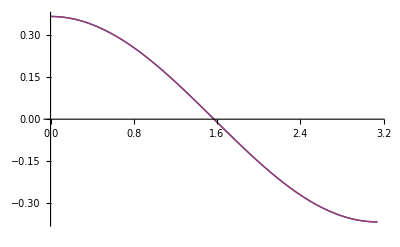

```mathematica
Plot[{ψ[a,θ,1],Cos[θ]Exp[-1]},{θ,0,Pi}]
```

Animation of the solution, evaluated along the z axis:

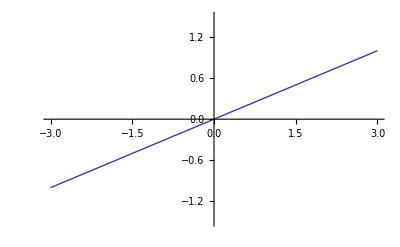
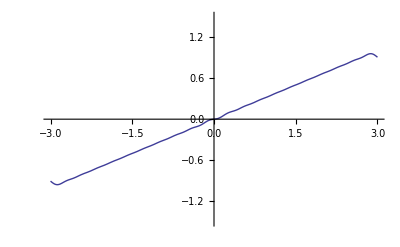
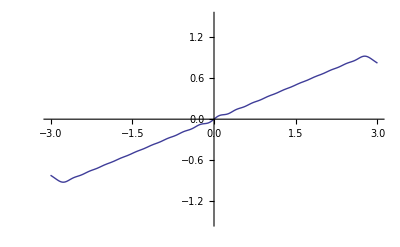
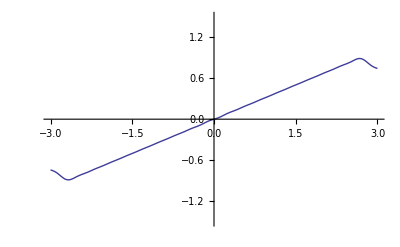
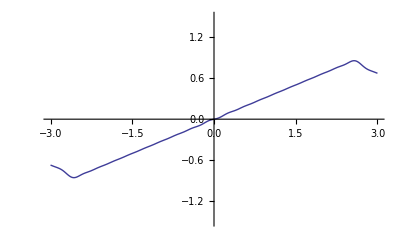
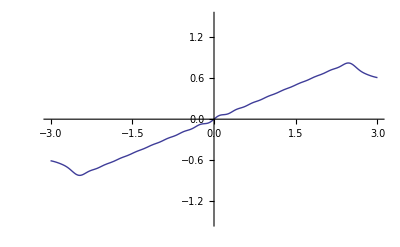
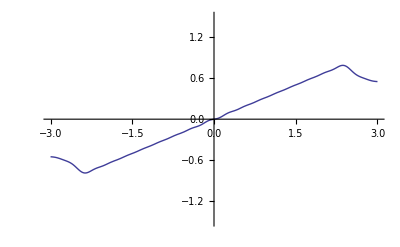
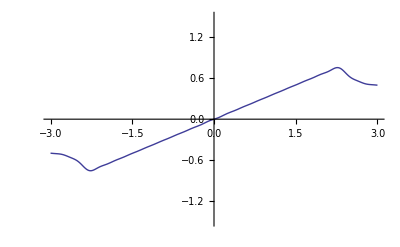

```mathematica
Table[p1=Plot[ψ[r,0,t],{r,0,a},PlotRange->{-1.5,1.5}];p2=ParametricPlot[{-r,ψ[r,Pi,t]},{r,0,a},PlotRange->{-1.5,1.5}];Show[p1,p2,PlotRange->{{-a,a},{-1.5,1.5}}],{t,0,6,.1}]
```

```mathematica
ListAnimate[%]
```